# Universal Portfolios

### Representing the stock market with vectors

Let’s represent the performance of a collection of 2 stocks using a 2 dimensional vector. A sequence of these vectors r_1,...,r_n where r_i=(r_i1, r_(i2,)) denotes the performance of the two stocks in periods 1 to n.

#### Example

Let’s imagine these are the returns for two stocks over 3 periods:
r_1= (1,1.2)
r_2= (0.9,1.1)
r_3= (1.3,0.95)

Then assuming that the portfolio is invested 50% on each stock, the return of the portfolio at the end will be

∏_(i=1)^3 r_i*(0.5,0.5)
=(1*0.5 + 1.2*0.5)*(0.9*0.5+1.1*0.5)*(1.3*0.5+0.95*0.5)
 = 1.2375

Which interestingly is higher than both the returns of investing only on stock 1 or 2:

Returns for stock 1: 
1*0.9*1.3=1.17

Returns for stock 2:
1.2*1.1*0.95=1.254

### Representing portfolios with vectors

A portfolio of stocks is, in essence, a way of dividing your total wealth among all available stocks. We can therefore represent a portfolio over time, composed of two stocks, by using sequence of vectors p_1,... p_n where p_i=(p,1-p) is the fraction of capital allocated to the first and second stocks in the i-th period.

#### Example

The reason why we use a vector to represent the portfolio, is that if we have a vector of returns r_i=(1.2,0.9) and a portfolio vector of p_i=(0.2,0.8) the return for that period is simply the product of the vectors: r_i p_i=1.2*0.2 + 0.9*0.8 

This means we can represent the returns of the portfolio at step n as follows:

W_n(p)=∏_(i=1)^n r_i p

Or equivalently

W_n(p)=∏_(i=1)^n (r_i1 p + r_i2(1-p))

So W_n denotes the factor by which your wealth would grow by period n had it been invested using the given portfolio weights and stock returns.

### What is the Universal Portfolio?

The universal portfolio is a portfolio that, given enough time, will beat the portfolio composed of the stock that had the best returns. So imagine you could look into the future and you could tell that over the next 10 years, the best performing stock will be, say Microsoft. The Universal Portfolio will, with high probability beat a portfolio composed only of Microsoft, without having to peak at the future.

Let’s define the universal portfolio now:

(p̂)_k= ((p̂)_k,1-(p̂)_k)

Where

(p̂)_1=0.5 and (p̂)_k = (∫_0^1 p W_n(p)ⅆp)/(∫_0^1 W_n(p)ⅆp)

Which means we initially spread out our allocations evenly and on the next step we adjust each allocation by the formula in (p̂)_k.

#### Example

Consider the following market returns

r_1= (1,1.2)
r_2= (0.9,1.1)
r_3= (1.3,0.95)

At n=1
By definition,  (p̂)_1=0.5  and W_1=1 so (p̂)_1=(0.5,0.5)

At n=2

(p̂)_2 = (∫_0^1 p (1p + 1.2(1-p))ⅆp)/(∫_0^1 (1p + 1.2(1-p))ⅆp)
=0.55/1.1
=

```mathematica
Wealth[returns_, portfolios_]:=∏_(i=1)^Length[returns] (returns[[i]].portfolios[[i]]);

ConstantPortfolio[portfolio_,n_]:=Table[portfolio,{i,1,n}];

UniversalPortfolio[returns_]:=With[
{portfolios = ConstantPortfolio[{p,1-p},Length[returns]]},
(∫_0^1 p*Wealth[returns,portfolios]ⅆp)/(∫_0^1 Wealth[returns,portfolios]ⅆp)
];
```

```mathematica
UniversalPortfolioWeights[returns_]:=ParallelTable[
With[
{p=UniversalPortfolio[Take[returns, i]]},
If[Mod[i,20]==0,Print["done with" <> ToString[i]]];
{p,1-p}],
{i,1,Length[returns]}
]
```

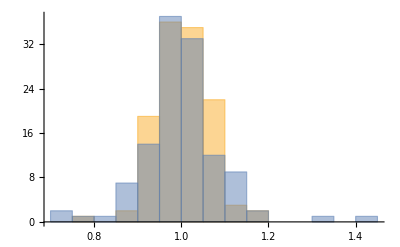

```mathematica
stock1 = FinancialData["NYSE:IBM","Return",{Today-Quantity[10,"Years"],Today,"Month"}]["Values"]//Map[1+#&];
stock2 = FinancialData["NYSE:GE","Return",{Today-Quantity[10,"Years"],Today,"Month"}]["Values"]//Map[1+#&];

Histogram[{stock1,stock2}]
```

```mathematica
returns = Table[{stock1[[i]],stock2[[i]]},{i,1,Length[stock1]}];
Length[returns]
```

120

(0.997753 (1-a)+0.845133 a) (0.927684 (1-a)+0.871493 a) 5255 (1.02007 (1-a)+1.12024 a) (1.02236 (1-a)+1.125 a)
 |  |  |  |

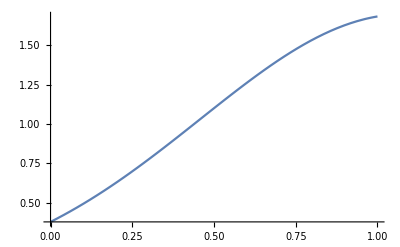

```mathematica
x=Wealth[returns,ConstantPortfolio[{a,1-a},Length[returns]]]
Plot[x,{a,0,1}]
```

```mathematica
weights=UniversalPortfolioWeights[Take[returns,100]]
```

done with20

done with40

done with60

done with80

done with100

{{0.490395,0.509605},{0.490598,0.509402},{0.487136,0.512864},{0.491281,0.508719},{0.493385,0.506615},{0.49631,0.50369},{0.500291,0.499709},{0.509441,0.490559},{0.512922,0.487078},{0.519311,0.480689},{0.516065,0.483935},{0.521965,0.478035},{0.509515,0.490485},{0.509734,0.490266},{0.509594,0.490406},{0.510148,0.489852},{0.511574,0.488426},{0.508136,0.491864},{0.501273,0.498727},{0.501803,0.498197},{0.501837,0.498163},{0.498755,0.501245},{0.49968,0.50032},{0.497845,0.502155},{0.498296,0.501704},{0.498193,0.501807},{0.493513,0.506487},{0.498876,0.501124},{0.497613,0.502387},{0.496463,0.503537},{0.489214,0.510786},{0.486785,0.513215},{0.485881,0.514119},{0.483908,0.516092},{0.473762,0.526238},{0.472788,0.527212},{0.471537,0.528463},{0.475619,0.524381},{0.478117,0.521883},{0.479972,0.520028},{0.47853,0.52147},{0.47406,0.52594},{0.47358,0.52642},{0.481831,0.518169},{0.479904,0.520096},{0.479298,0.520702},{0.466853,0.533147},{0.464152,0.535848},{0.466398,0.533602},{0.467278,0.532722},{0.464678,0.535322},{0.467765,0.532235},{0.465917,0.534083},{0.465177,0.534823},{0.463171,0.536829},{0.464298,0.535702},{0.461632,0.538368},{0.457952,0.542048},{0.444076,0.555924},{0.44165,0.55835},{0.436813,0.563187},{0.434422,0.565578},{0.438427,0.561573},{0.443096,0.556904},{0.442789,0.557211},{0.449166,0.550834},{0.444242,0.555758},{0.449719,0.550281},{0.449272,0.550728},{0.452963,0.547037},{0.451718,0.548282},{0.45233,0.54767},{0.451396,0.548604},{0.460554,0.539446},{0.462696,0.537304},{0.460099,0.539901},{0.455589,0.544411},{0.457051,0.542949},{0.458127,0.541873},{0.45746,0.54254},{0.460841,0.539159},{0.462431,0.537569},{0.482308,0.517692},{0.491099,0.508901},{0.494115,0.505885},{0.505734,0.494266},{0.513048,0.486952},{0.515528,0.484472},{0.507328,0.492672},{0.506071,0.493929},{0.507184,0.492816},{0.510088,0.489912},{0.516119,0.483881},{0.529108,0.470892},{0.516104,0.483896},{0.547047,0.452953},{0.538986,0.461014},{0.528709,0.471291},{0.530054,0.469946},{0.534959,0.465041}}

```mathematica
Wealth[Take[returns,100],weights]
```

1.13475

```mathematica
Wealth[Take[returns,100],ConstantPortfolio[{p,1-p},100]]
```

(0.894597 (1-p)+0.763375 p) (1.00742 (1-p)+0.866038 p) (0.934189 (1-p)+0.906772 p) (1.01065 (1-p)+0.914702 p) (1.00255 (1-p)+0.91871 p) (0.972819 (1-p)+0.920466 p) (0.950958 (1-p)+0.92055 p) (0.974974 (1-p)+0.935454 p) (0.927345 (1-p)+0.93772 p) (0.949528 (1-p)+0.939235 p) (0.948167 (1-p)+0.940454 p) (0.896539 (1-p)+0.941942 p) (0.996281 (1-p)+0.943815 p) (1.04377 (1-p)+0.944796 p) (0.9641 (1-p)+0.949555 p) (0.910664 (1-p)+0.949605 p) (0.94539 (1-p)+0.95556 p) (0.982518 (1-p)+0.958798 p) (0.944464 (1-p)+0.961545 p) (0.87983 (1-p)+0.961599 p) (0.967285 (1-p)+0.963618 p) (1.14671 (1-p)+0.966269 p) (0.982444 (1-p)+0.967517 p) (1.09418 (1-p)+0.967761 p) (0.999665 (1-p)+0.968413 p) (1.13631 (1-p)+0.978085 p) (1.02534 (1-p)+0.980256 p) (1.00332 (1-p)+0.981418 p) (0.988977 (1-p)+0.983239 p) (0.955351 (1-p)+0.984599 p) (1.00071 (1-p)+0.985552 p) (1.04825 (1-p)+0.987089 p) (0.994421 (1-p)+0.987155 p) (1.04917 (1-p)+0.987251 p) (0.975341 (1-p)+0.988607 p) (0.962672 (1-p)+0.989332 p) (0.954598 (1-p)+0.991108 p) (0.975585 (1-p)+0.992475 p) (1.0507 (1-p)+0.993151 p) (1.02635 (1-p)+0.993156 p) (0.960391 (1-p)+0.994725 p) (0.982311 (1-p)+0.995881 p) (0.960642 (1-p)+0.996428 p) (1.00321 (1-p)+0.997713 p) (1.00702 (1-p)+0.997997 p) (0.998072 (1-p)+0.99848 p) (0.95861 (1-p)+0.999099 p) (0.955474 (1-p)+0.999811 p) (0.995681 (1-p)+1.00205 p) (1.0458 (1-p)+1.00317 p) (1.03527 (1-p)+1.00465 p) (0.958413 (1-p)+1.00735 p) (1.00234 (1-p)+1.00779 p) (0.994667 (1-p)+1.00786 p) (1.01989 (1-p)+1.00794 p) (1.033 (1-p)+1.00922 p) (0.907242 (1-p)+1.00939 p) (1.10117 (1-p)+1.01389 p) (0.994807 (1-p)+1.01433 p) (0.968097 (1-p)+1.01551 p) (1.04043 (1-p)+1.01597 p) (0.941875 (1-p)+1.01722 p) (1.05088 (1-p)+1.02056 p) (1.03862 (1-p)+1.02068 p) (0.961501 (1-p)+1.0215 p) (0.949376 (1-p)+1.02166 p) (0.952125 (1-p)+1.02233 p) (1.03506 (1-p)+1.02324 p) (1.02714 (1-p)+1.02541 p) (1.04621 (1-p)+1.03182 p) (0.880745 (1-p)+1.03229 p) (1.00147 (1-p)+1.03744 p) (1.16436 (1-p)+1.03747 p) (1.01173 (1-p)+1.03856 p) (1.01649 (1-p)+1.03953 p) (1.02264 (1-p)+1.03971 p) (1.05985 (1-p)+1.04391 p) (1.01995 (1-p)+1.04605 p) (1.04467 (1-p)+1.04742 p) (0.939873 (1-p)+1.05139 p) (1.02241 (1-p)+1.05375 p) (1.0979 (1-p)+1.05581 p) (0.957001 (1-p)+1.05737 p) (0.989199 (1-p)+1.05824 p) (0.949629 (1-p)+1.06004 p) (1.06146 (1-p)+1.06014 p) (1.05354 (1-p)+1.06059 p) (1.00925 (1-p)+1.06075 p) (0.833747 (1-p)+1.0619 p) (0.995693 (1-p)+1.06209 p) (0.983089 (1-p)+1.06346 p) (1.09791 (1-p)+1.06371 p) (1.10488 (1-p)+1.06467 p) (1.05704 (1-p)+1.06502 p) (0.926648 (1-p)+1.06701 p) (1.0915 (1-p)+1.06723 p) (0.742574 (1-p)+1.09028 p) (1.10115 (1-p)+1.10384 p) (1.09094 (1-p)+1.15584 p) (1.34214 (1-p)+1.18255 p)